```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[ListLinePlot,Frame-> True,PlotStyle-> Black,GridLines-> Automatic,PlotMarkers-> Automatic];
```

```mathematica
a=Import["fitness_history.csv","Table"];
```

```mathematica
bestfit=Transpose[a][[1]];
avgfit=Transpose[a][[2]];
```

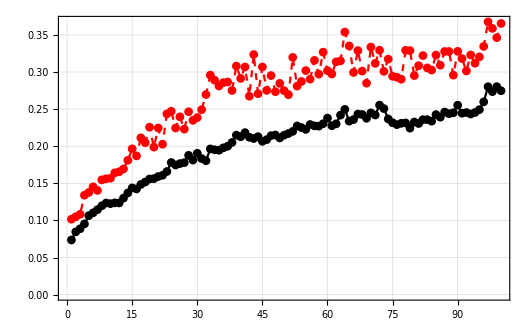

```mathematica
ap=ListLinePlot[avgfit];
bp=ListLinePlot[bestfit,PlotStyle->{Red, Dashed}];
Show[{bp,ap}]
```

```mathematica
(* Avg error per entry *)
√(1/(Max[bestfit] 257))
```

0.102887